```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->-t]
```

```mathematica
T[t_,m_]:=T[t,m]=t*IdentityMatrix[m]
```

```mathematica
Clear[LEFT,leads]
```

```mathematica
leads[size_]:=Table[ToExpression[Import["/home/shardul/PhD_new/PhD/fwi/sq_lattice/leads/size_"<>ToString[size]<>"_lead_"<>ToString[x]<>"_.dat"]],{x,Range[0,2,0.01]}]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]=leads[[Round[ω*100+251]]]
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-g[ω,δ,t,ϵ,m].T[t,m].LEFT[ω,δ,t,ϵ,m].T[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-g[ω,δ,t,ϵ,m].T[t,m].LEFT[ω,δ,t,ϵ,m].T[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-SL[ω,δ,t,ϵ,m].T[t,m].SR[ω,δ,t,ϵ,m].T[t,m]].SL[ω,δ,t,ϵ,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-SR[ω,δ,t,ϵ,m].T[t,m].SL[ω,δ,t,ϵ,m].T[t,m]].SR[ω,δ,t,ϵ,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:= SR[ω,δ,t,ϵ,m].T[t,m].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,m_]:= Abs[Tr[gdd[ω,δ,t,ϵ,m].T[t,m].grr[ω,δ,t,ϵ,m].T[t,m]-T[t,m].GNON[ω,δ,t,ϵ,m].T[t,m].GNON[ω,δ,t,ϵ,m]]]
```

```mathematica
pris=Compile[{ω},tr[ω,0.0001,5,0,100],CompilationTarget->"C",Parallelization->True]
```

CompiledFunction[…]

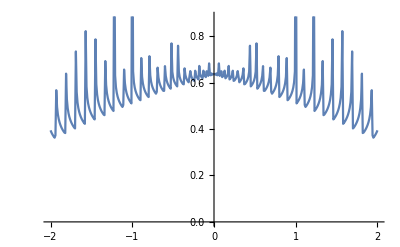

```mathematica
ListLinePlot[Table[{ω,-Im[IL[ω,0.0001,1,0,50][[1,1]]]},{ω,Range[-2,2,0.01]}]]
```

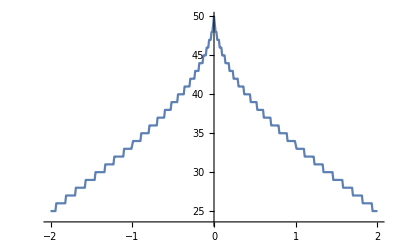

```mathematica
ListLinePlot[Table[{ω,tr[ω,0.0001,1,0,50]},{ω,Range[-2,2,0.01]}]]
```

```mathematica
Clear[LEFT1]
```

```mathematica
leads1=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/sq_lattice/10sq/leads/lead_"<>ToString[x]<>".dat"]],{x,Range[-2.5,2.5,0.01]}]
```

{{{-0.497785-0.228643 ⅈ,0.130706+0.28624 ⅈ,0.0767826-0.159852 ⅈ,4,-0.0005428+0.0336017 ⅈ,0.0176555+0.0146533 ⅈ,-0.0134474-0.034101 ⅈ},{1},6,{1},{1}},500}
 |  |  |  |

```mathematica
LEFT1[ω_,δ_,t_,ϵ_,m_]:=LEFT1[ω,δ,t,ϵ,m]= leads1[[Round[ω*100+251]]]
```

```mathematica
F[n_]:= {n,n}
```

```mathematica
unit[ω_,δ_,t_,ϵ_,ϵ1_,n_]:=Module[{b=β[ω,δ,t,ϵ,50]},ReplacePart[b,Table[F[RandomSample[{RandomInteger[{2,49}]},1]]//Flatten,n]->ω+ⅈ*δ-ϵ1]]
```

```mathematica
device[ω_,δ_,t_,ϵ_,ϵ1_,m_,num_,n_]:=Module[{Tin=T[1,m],list,b2},
list={RandomSample[Join[Table[unit[ω,0.0001,1,0,ϵ1,n],num],Table[unit[ω,0.0001,1,0,0,1],10-num]]]};
sl1= Module[{J=SL[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[m]-Inverse[ReplacePart[list[[1,ζ]],{{1,1},{50,50}}->ω+ⅈ*δ-t*t*LEFT1[ω,δ,t,ϵ,10][[ζ,ζ]]]].ConjugateTranspose[Tin].J.Tin].Inverse[ReplacePart[list[[1,ζ]],{{1,1},{50,50}}->ω+ⅈ*δ-t*t*LEFT1[ω,δ,t,ϵ,10][[ζ,ζ]]]],{ζ,1,10}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.Tin.SL[ω,0.0001,1,0,m].Tin].sl1;
Ir1:=Inverse[IdentityMatrix[m]-SL[ω,0.0001,1,0,m].Tin.sl1.Tin].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].Tin.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.Tin.grr1.Tin-Tin.GNON1.Tin.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.Tin.grr1.Tin-Tin.GNON1.Tin.GNON1]]]]
```

```mathematica
Range[1,19,2]
```

{1,3,5,7,9,11,13,15,17,19}

```mathematica
transmission= Table[Import["/home/shardulmukim/PhD/fwi/sq_lattice/50sq/CA_10_sec_"<>ToString[x]<>".dat"],{x,Range[1,20,1]}]
```

{{{-0.5,38.4739},{-0.49,38.521},{-0.48,38.5379},{-0.47,38.5294},{-0.46,38.4749},{-0.45,38.2378},{-0.44,38.8793},{-0.43,39.3612},{-0.42,39.4658},{-0.41,39.5085},{-0.4,39.5205},{-0.39,39.4986},{-0.38,39.3883},76,{0.39,39.4198},{0.4,39.4535},{0.41,39.4469},{0.42,39.4005},{0.43,39.2922},{0.44,38.7925},{0.45,38.0718},{0.46,38.3902},{0.47,38.4663},{0.48,38.4819},{0.49,38.4665},{0.5,38.421}},18,{1}}
 |  |  |  |

```mathematica
transmission//Dimensions
```

{20,101,2}

```mathematica
input= Table[ParallelTable[{ω,device[ω,0.0001,1,0,0.5,50,5,2]},{ω,Range[-0.5,0.5,0.01]}],100]
```

{{{-0.5,37.4868},{-0.49,37.5494},{-0.48,37.59},{-0.47,37.4709},{-0.46,37.3965},{-0.45,37.5002},90,{0.46,35.3294},{0.47,37.0995},{0.48,37.243},{0.49,37.1054},{0.5,37.0934}},98,{1}}
 |  |  |  |

```mathematica
misfit[x_,y_,n_]:=Module[{m5=input[[n]]},
ρ1:=Table[Module[{B1=Transpose[{m5[[1;;101]][[;;,1]],(m5[[1;;101,2]]-transmission[[f]][[1;;101,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)],{f,20}];
list=Transpose[Join[{Range[1,20,1]},{ρ1}]];list[[Position[list,Min[list]][[1,1]]]][[1]]]
```

```mathematica
Table[misfit[0.5,-0.5,n],{n,100}]
```

{10,10,10,8,11,9,11,11,8,8,11,11,11,11,9,10,10,9,11,9,7,9,9,11,12,10,10,10,11,9,8,9,10,12,10,10,9,10,8,11,10,9,10,9,10,11,12,10,10,10,11,11,11,10,10,9,10,11,7,9,10,13,10,10,11,11,11,9,11,12,12,10,11,11,9,11,8,10,9,10,9,10,9,8,11,12,9,8,10,10,11,10,8,10,11,9,12,9,8,9}

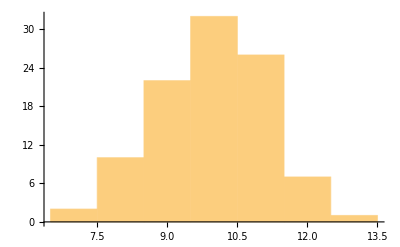

```mathematica
Histogram[%70]
```

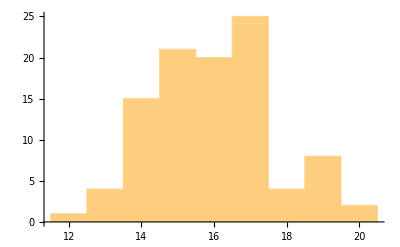

```mathematica
Histogram[%66]
```

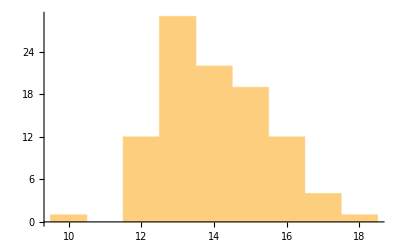

```mathematica
Histogram[%62]
```

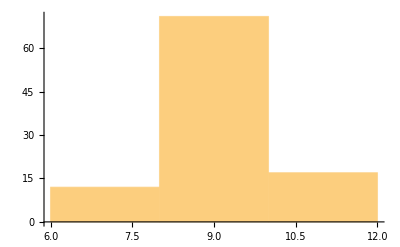

```mathematica
Histogram[%54]
```

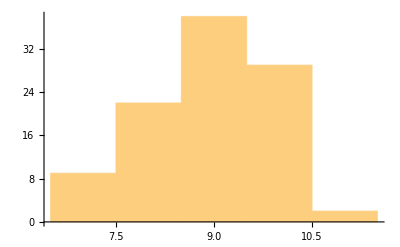

```mathematica
Histogram[%43]
```

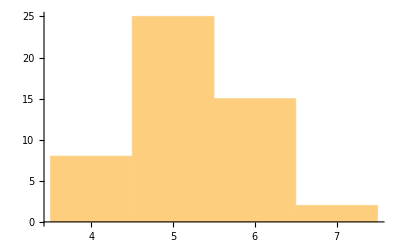

```mathematica
Histogram[{4,5,5,6,4,5,5,4,6,4,6,5,7,4,5,6,6,6,5,6,5,6,5,5,6,5,6,6,5,6,5,5,6,5,5,6,6,5,5,5,4,5,5,5,5,7,4,5,4,5}]
```

```mathematica
N[29/450]
```

0.0644444

```mathematica
N[1/40]
```

0.025

```mathematica
N[8/175]
```

0.0457143

```mathematica
N[1/150]
```

0.00666667

```mathematica
N[1/50]
```

0.02

```mathematica
N[1/20]
```

0.05

```mathematica
N[13/250]
```

0.052

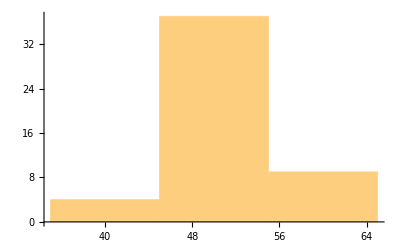

```mathematica
Histogram[{50,40,60,60,50,50,60,60,50,60,50,50,50,50,50,50,40,40,50,50,50,50,50,50,50,50,40,60,50,50,50,50,50,50,60,50,50,60,50,50,50,50,50,60,50,50,50,50,50,50}]
```

```mathematica
Tally[{5,3,3,7,7,3,13,23,5,23,11,23,17,13,7,17,3,7,17,9,11,5,7,7,11,7,3,13,3,5,3,17,13,15,13,5,7,5,15,5,5,7,5,17,7,5,23,3,7,17}]
```

{{5,10},{3,8},{7,11},{13,5},{23,4},{11,3},{17,6},{9,1},{15,2}}

```mathematica
misfit1[x_,y_,n_]:=Module[{m5=input[[n]]},
ρ1:=Table[Module[{B1=Transpose[{m5[[1;;101]][[;;,1]],(m5[[1;;101,2]]-transmission[[f]][[1;;101,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)],{f,10}];
ρ1]
```

```mathematica
Table[misfit1[0.5,-0.5,n],{n,100}]
```

{{0.31979,0.0896033,0.0402443,0.0735708,0.152241,0.263771,0.395048,0.525894,0.604874,0.68865},{0.428529,0.146556,0.0651692,0.0817088,0.153345,0.26407,0.395785,0.530043,0.616536,0.705688},{0.40085,0.12935,0.0647148,0.100661,0.188602,0.309745,0.450154,0.585187,0.664711,0.749146},{0.33516,0.104753,0.039778,0.0470615,0.100786,0.187968,0.298513,0.418665,0.505178,0.594395},{0.373669,0.106663,0.0371081,0.0604258,0.137051,0.245624,0.375243,0.50468,0.587313,0.675132},{0.323614,0.0871124,0.0389329,0.0774072,0.165779,0.284981,0.423603,0.558012,0.638371,0.723933},{0.34998,0.10979,0.0443444,0.0588189,0.121857,0.220244,0.339982,0.467473,0.552465,0.641069},{0.417008,0.200378,0.145962,0.160717,0.223294,0.319322,0.436594,0.561802,0.654748,0.748528},{0.298405,0.0702837,0.0222969,0.0559688,0.137983,0.250227,0.382178,0.515663,0.599758,0.688683},{0.313549,0.0768506,0.0280069,0.063357,0.145745,0.256038,0.38571,0.512396,0.588422,0.671071},{0.420143,0.13517,0.0544869,0.0740225,0.147901,0.259898,0.393168,0.523124,0.605215,0.689671},{0.362195,0.103708,0.0325406,0.0477814,0.115288,0.220911,0.34817,0.477644,0.563294,0.651525},{0.402625,0.137006,0.0689176,0.0913164,0.159909,0.257939,0.378249,0.500692,0.575502,0.65893},{0.349284,0.101652,0.0430332,0.0707593,0.148014,0.260727,0.393372,0.527456,0.610318,0.698133},{0.276519,0.0643576,0.015838,0.0366768,0.0985568,0.190924,0.304828,0.42767,0.509286,0.596257},{0.338709,0.168912,0.119002,0.109624,0.132832,0.18844,0.268638,0.372236,0.455665,0.542162},{0.29862,0.0845547,0.0488319,0.0924771,0.185733,0.310479,0.4524,0.593199,0.683291,0.776221},{0.361387,0.119176,0.055425,0.0712142,0.130945,0.222632,0.338538,0.461337,0.540733,0.627394},{0.384232,0.112818,0.0403575,0.0619044,0.138668,0.25109,0.385368,0.521511,0.610206,0.703231},{0.402154,0.131747,0.0468471,0.0461606,0.09614,0.184545,0.297524,0.421721,0.512166,0.605165},{0.232738,0.0477808,0.0264352,0.0717314,0.158274,0.269364,0.399815,0.533201,0.616102,0.706687},{0.375573,0.119228,0.0476813,0.0603128,0.1249,0.22841,0.352942,0.483591,0.573692,0.665361},{0.302187,0.0816516,0.0295362,0.050957,0.115332,0.21382,0.333859,0.461655,0.546,0.634741},{0.267976,0.116161,0.109885,0.157149,0.232536,0.322738,0.43389,0.549781,0.618192,0.698576},{0.438686,0.14969,0.066593,0.0841952,0.155325,0.263123,0.392705,0.524098,0.607774,0.695264},{0.441539,0.199452,0.14093,0.162488,0.236304,0.337261,0.45981,0.584967,0.669053,0.759094},{0.385337,0.117298,0.0483967,0.0750824,0.153824,0.269324,0.405044,0.540448,0.624775,0.712502},{0.408695,0.129611,0.0572382,0.0843274,0.166022,0.285316,0.42451,0.563014,0.650636,0.741197},{0.376674,0.132894,0.0796557,0.113598,0.190501,0.293913,0.417931,0.542018,0.615419,0.696936},{0.377924,0.107272,0.0334949,0.0525086,0.121254,0.223008,0.346375,0.468871,0.544443,0.625744},{0.349731,0.0977354,0.0234215,0.0279884,0.0803378,0.167431,0.27872,0.40037,0.485665,0.575052},{0.432057,0.141968,0.0513259,0.055471,0.114165,0.21056,0.331518,0.458929,0.545095,0.635211},{0.416401,0.262209,0.228274,0.23544,0.281828,0.360404,0.460934,0.583611,0.683065,0.782814},{0.453706,0.143704,0.0470837,0.0542701,0.120171,0.226325,0.355155,0.483426,0.56635,0.652707},{0.489147,0.299287,0.239019,0.225537,0.253721,0.31549,0.402354,0.514098,0.609571,0.706028},{0.257996,0.0813837,0.0477229,0.0705747,0.131227,0.22432,0.337836,0.462297,0.545936,0.633703},{0.263625,0.0828151,0.061215,0.107123,0.192873,0.310928,0.445898,0.58244,0.665251,0.751942},{0.342682,0.165057,0.14256,0.178249,0.25547,0.354671,0.474316,0.601288,0.687661,0.781147},{0.403421,0.129494,0.050195,0.0604992,0.126747,0.22722,0.351393,0.477448,0.563592,0.652895},{0.243225,0.063147,0.0349926,0.0671939,0.139534,0.240067,0.360399,0.488418,0.575068,0.666131},{0.410064,0.178509,0.124085,0.144699,0.216358,0.320246,0.444617,0.573806,0.663853,0.757104},{0.411826,0.129832,0.0544753,0.0806605,0.162115,0.281217,0.420058,0.556954,0.644151,0.733444},{0.320589,0.0875208,0.0380029,0.0725418,0.154051,0.266711,0.400413,0.537425,0.623278,0.715481},{0.370288,0.122169,0.0573024,0.0784417,0.145606,0.248101,0.371878,0.500407,0.585471,0.672908},{0.458514,0.162795,0.072609,0.0783732,0.14006,0.241669,0.365373,0.492797,0.582433,0.673139},{0.374805,0.131039,0.0643283,0.0760028,0.138375,0.23883,0.361616,0.490349,0.582063,0.674621},{0.45325,0.146045,0.0441823,0.0408452,0.0950923,0.189921,0.309623,0.435665,0.523364,0.613706},{0.408007,0.140307,0.0645611,0.0751762,0.13937,0.242764,0.367449,0.496036,0.582953,0.672136},{0.307214,0.0895336,0.0306556,0.0396653,0.0915704,0.176934,0.285282,0.403825,0.488624,0.575863},{0.370371,0.184726,0.142219,0.153108,0.205691,0.285481,0.386439,0.499871,0.583501,0.671008},{0.470298,0.173556,0.0810081,0.0843572,0.143205,0.242656,0.366778,0.496507,0.582664,0.673322},{0.391155,0.153559,0.0938676,0.111843,0.18089,0.280133,0.401234,0.526716,0.613283,0.704197},{0.312377,0.0794892,0.023152,0.0455519,0.112274,0.210015,0.329298,0.454672,0.537894,0.625741},{0.342264,0.0969554,0.028905,0.039728,0.100756,0.201041,0.323358,0.453749,0.544273,0.636808},{0.335221,0.155856,0.124403,0.148879,0.215197,0.307977,0.420857,0.541741,0.627359,0.716828},{0.42118,0.20553,0.160643,0.184362,0.256187,0.355752,0.477611,0.605948,0.69441,0.789268},{0.427662,0.196479,0.145567,0.173783,0.256291,0.374598,0.511775,0.650371,0.745888,0.842267},{0.297368,0.0759227,0.0335844,0.068488,0.145208,0.247666,0.370803,0.497447,0.575015,0.661061},{0.233164,0.0724066,0.054245,0.091252,0.161858,0.261846,0.380627,0.50832,0.58903,0.675524},{0.389659,0.123311,0.0592621,0.0925252,0.180511,0.303452,0.445316,0.581497,0.662427,0.747088},{0.412791,0.188873,0.143083,0.175558,0.261707,0.381056,0.51932,0.655871,0.747356,0.840825},{0.370303,0.143979,0.0865156,0.10134,0.164596,0.261106,0.378637,0.502318,0.59076,0.681171},{0.297787,0.0802918,0.0310016,0.0548685,0.119772,0.215305,0.331289,0.450622,0.526061,0.606745},{0.313466,0.0898073,0.050034,0.0936559,0.183934,0.30524,0.445949,0.585592,0.668939,0.758514},{0.30487,0.102448,0.0605217,0.0849426,0.149908,0.246517,0.363859,0.489533,0.569841,0.656484},{0.411723,0.145257,0.0551871,0.0444336,0.0865146,0.170403,0.279062,0.401514,0.494402,0.588161},{0.379801,0.132984,0.0739084,0.0981626,0.172016,0.274055,0.398035,0.524757,0.609107,0.699805},{0.415946,0.136579,0.0538898,0.0619121,0.116804,0.205022,0.317201,0.434025,0.509068,0.591243},{0.388742,0.1137,0.039214,0.0610118,0.137985,0.251607,0.385575,0.515761,0.597652,0.682516},{0.301449,0.0847251,0.0520569,0.10238,0.195181,0.316303,0.455153,0.590765,0.668721,0.753442},{0.271332,0.0614474,0.0281726,0.0709835,0.156523,0.266592,0.396282,0.524993,0.603785,0.690008},{0.324102,0.0906417,0.0372521,0.064897,0.136816,0.23926,0.36183,0.48911,0.571214,0.658342},{0.205706,0.0438506,0.0263505,0.0650743,0.141485,0.247214,0.370749,0.500072,0.584751,0.672967},{0.319103,0.0960171,0.0346326,0.0392355,0.0862296,0.165026,0.267647,0.381931,0.462561,0.548444},{0.379298,0.112011,0.0372232,0.0536601,0.127054,0.237724,0.370275,0.50307,0.590848,0.680557},{0.395204,0.124226,0.0527248,0.0753152,0.153383,0.267927,0.402529,0.533667,0.615073,0.699896},{0.28161,0.0710902,0.0329306,0.0718684,0.152229,0.26303,0.392431,0.523786,0.605137,0.691347},{0.37903,0.177702,0.123106,0.13148,0.180705,0.270276,0.380317,0.503092,0.590268,0.677424},{0.318863,0.126446,0.0827234,0.0979562,0.152513,0.239599,0.348679,0.471397,0.563341,0.657445},{0.353154,0.0989954,0.0354964,0.0610671,0.139937,0.25173,0.383894,0.515908,0.601124,0.690073},{0.305325,0.129877,0.0953333,0.120093,0.18653,0.287751,0.408057,0.538204,0.628154,0.71879},{0.443607,0.153556,0.0686476,0.0845484,0.153597,0.256873,0.383438,0.510611,0.591135,0.676482},{0.343679,0.0966479,0.0379957,0.0667141,0.146128,0.263653,0.400762,0.538707,0.627088,0.717508},{0.423059,0.145065,0.0702568,0.0912709,0.166505,0.279982,0.414005,0.545643,0.627107,0.712004},{0.427201,0.134962,0.0455174,0.0537476,0.116381,0.218978,0.343486,0.470309,0.553057,0.638529},{0.37209,0.112122,0.0399424,0.0544722,0.121171,0.226032,0.352478,0.482585,0.568617,0.656907},{0.273519,0.063003,0.0268549,0.0672219,0.155075,0.273715,0.411487,0.549133,0.637064,0.728945},{0.236812,0.0587314,0.0314003,0.0651805,0.137274,0.233176,0.349178,0.469226,0.544597,0.62701},{0.388506,0.221769,0.182126,0.19044,0.233077,0.315804,0.419657,0.5445,0.6403,0.734763},{0.31225,0.100981,0.0685564,0.116042,0.205676,0.319896,0.452702,0.580303,0.650026,0.729019},{0.275317,0.0647702,0.0287925,0.0695468,0.152769,0.264321,0.395314,0.527535,0.606906,0.693528},{0.392141,0.11517,0.0412456,0.0648128,0.144558,0.263235,0.40114,0.535993,0.621511,0.709109},{0.450606,0.210727,0.147865,0.161862,0.225151,0.322168,0.441358,0.567002,0.658886,0.752965},{0.365373,0.205262,0.160334,0.155016,0.185335,0.252867,0.344099,0.460548,0.552808,0.645537},{0.44507,0.148394,0.0569616,0.0646495,0.125464,0.225962,0.350543,0.478623,0.563282,0.651426},{0.338952,0.117293,0.0554104,0.0613263,0.113713,0.206308,0.321131,0.447883,0.539615,0.631856},{0.315561,0.0806688,0.0306432,0.0618817,0.13984,0.248027,0.375559,0.502694,0.582304,0.667502},{0.30284,0.0745702,0.0177758,0.0371604,0.102662,0.200648,0.320353,0.446428,0.531653,0.620659},{0.34387,0.156303,0.124061,0.154331,0.228479,0.32907,0.449016,0.575415,0.66393,0.755996},{0.316522,0.0840993,0.0288435,0.0526393,0.126112,0.233375,0.361878,0.497377,0.590572,0.686537}}

```mathematica
Table[Around[Table[%85[[x]][[y]],{x,100}]],{y,10}]
```

{0.360.06,0.120.05,0.070.05,0.090.04,0.160.04,0.260.05,0.380.05,0.510.05,0.590.06,0.680.06}

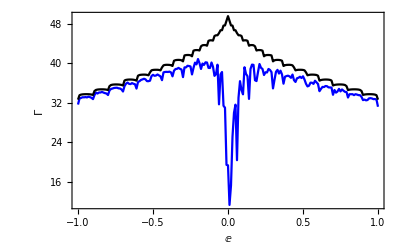

```mathematica
Show[ListLinePlot[ParallelTable[{ω,device[ω,0.0001,1,0,0.5,50,30,1]},{ω,Range[-1.,1.,0.01]}],PlotStyle->Blue,PlotRange->All,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}}],ListLinePlot[ParallelTable[{ω,device[ω,0.0001,1,0,0.0,50,30,1]},{ω,Range[-1.,1.,0.01]}],PlotStyle->{Black},PlotRange->All,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}}],PlotRange->All,FrameLabel->{{HoldForm[Γ],None},{HoldForm[E],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",15,GrayLevel[0]}]
```

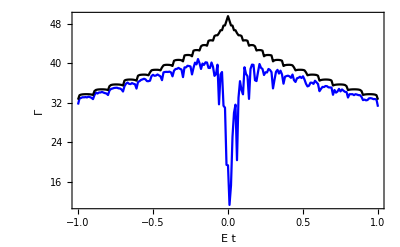

```mathematica
Show[%142,FrameLabel->{{HoldForm[Γ],None},{HoldForm[Ε t],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

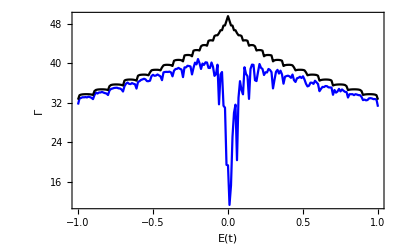

```mathematica
Show[%147,FrameLabel->{{HoldForm[Γ],None},{HoldForm[HoldForm[Ε[t]]],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",15,GrayLevel[0]}]
```

```mathematica
Show[%142,FrameLabel->{{HoldForm[Γ],None},{HoldForm[Ε(t)],None}},PlotLabel->None]
```

-Graphics-

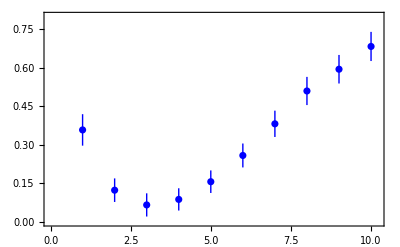

```mathematica
ListPlot[%86,Frame->True,PlotStyle->Blue,FrameTicks->{{Automatic,None},{Automatic,None}},PlotRange->{{0,10.2},{0,0.8}}]
```

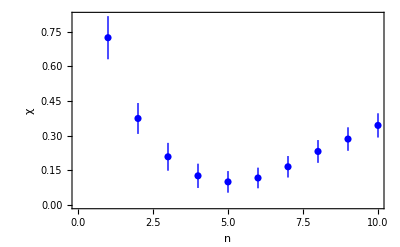

```mathematica
Show[%81,FrameLabel->{{HoldForm[χ],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",15,GrayLevel[0]}]
```

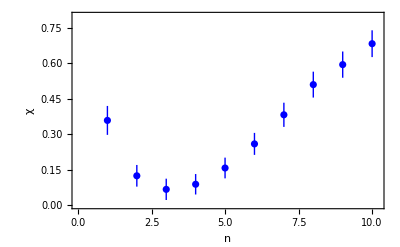

```mathematica
Show[%91,FrameLabel->{{HoldForm[χ],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",15,GrayLevel[0]},FrameLabel->{{HoldForm[χ],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",15,GrayLevel[0]}]
```

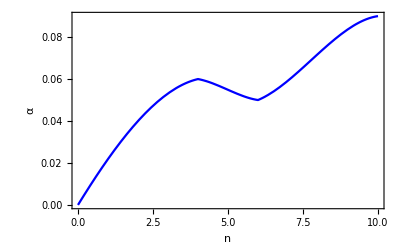

```mathematica
Show[%121,Frame->True,FrameLabel->{{HoldForm[α],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",15,GrayLevel[0]},FrameLabel->{{HoldForm[α],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",15,GrayLevel[0]}]
```

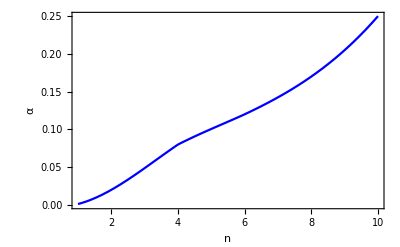

```mathematica
Show[%128,Frame->True,FrameLabel->{{HoldForm[α],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",15,GrayLevel[0]},FrameLabel->{{HoldForm[α],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",15,GrayLevel[0]}]
```

```mathematica
{{0,0},{2,0.02},{4,0.08},{6,0.12},{8,0.17},{10,0.25}}
```

{{0,0},{2,0.02},{4,0.08},{6,0.12},{8,0.17},{10,0.25}}

```mathematica
Interpolation[%124]
```

InterpolatingFunction[…]

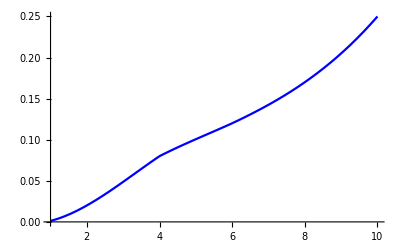

```mathematica
Plot[InterpolatingFunction[{{0.,10.}},{5,7,0,{6},{4},0,0,0,0,Automatic,{},{},False},{{0.,2.,4.,6.,8.,10.}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6},{0.,0.02,0.08,0.12,0.17,0.25}},{Automatic}][x],{x,1.,10.},PlotStyle->Blue]
```

```mathematica
Interpolation[%117]
```

InterpolatingFunction[…]

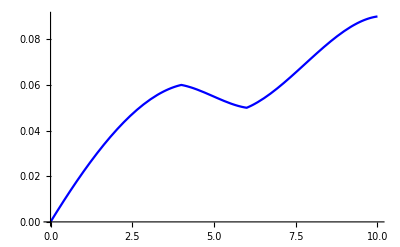

```mathematica
Plot[InterpolatingFunction[{{0.,10.}},{5,7,0,{6},{4},0,0,0,0,Automatic,{},{},False},{{0.,2.,4.,6.,8.,10.}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6},{0.,0.04,0.06,0.05,0.072,0.09}},{Automatic}][x],{x,0.,10.},PlotStyle->Blue]
```

```mathematica
FindFit[%101,a*Log[x]+b,{a,b},x]
```

{a→0.0262723,b→0.0190338}

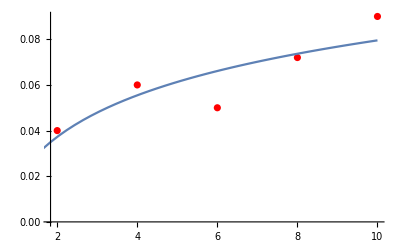

```mathematica
Show[ListPlot[%101,PlotStyle->Red],Plot[a Log[x]+b/.{a->0.026272272346114425,b->0.01903379111215903},{x,0,10}]]
```

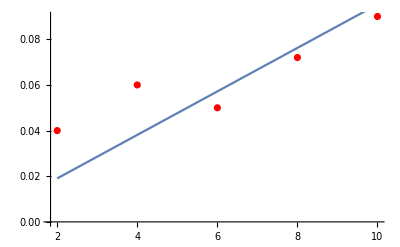

```mathematica
Show[ListPlot[%101,PlotStyle->Red],Plot[a x Log[b]/.{a->1.0210901328298843,b->1.0093741561570733},{x,2,10}]]
```

InterpolatingFunction::dmval: Input value {0.000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

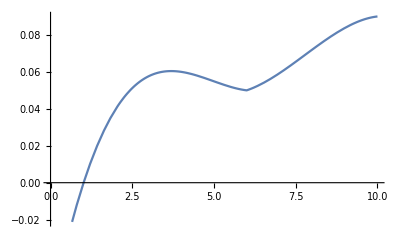

```mathematica
Plot[InterpolatingFunction[{{2.,10.}},{5,7,0,{5},{4},0,0,0,0,Automatic,{},{},False},{{2.,4.,6.,8.,10.}},{Developer`PackedArrayForm,{0,1,2,3,4,5},{0.04,0.06,0.05,0.072,0.09}},{Automatic}][x],{x,0,10.}]
```

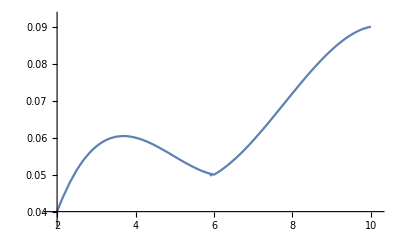

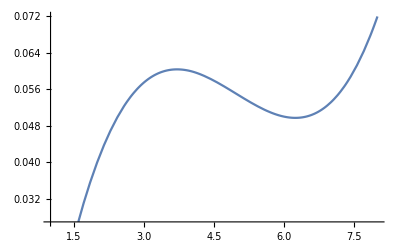

```mathematica
Plot[InterpolatingFunction[{{1.,8.}},{5,7,0,{5},{4},0,0,0,0,Automatic,{},{},False},{{1.,2.,4.,6.,8.}},{Developer`PackedArrayForm,{0,1,2,3,4,5},{0,0.04,0.06,0.05,0.072}},{Automatic}][x],{x,1.,8.}]
```

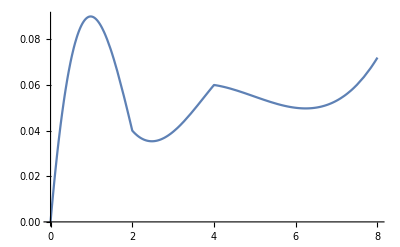

```mathematica
Plot[InterpolatingFunction[{{0.,8.}},{5,7,0,{6},{4},0,0,0,0,Automatic,{},{},False},{{0.,1.,2.,4.,6.,8.}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6},{0.,0.09,0.04,0.06,0.05,0.072}},{Automatic}][x],{x,0.,8.}]
```